The International Interaction Game

```mathematica
Clear[S,Subscript[F1, B̄],Subscript[F, B],R,Subscript[F1, A],Subscript[F1, Ā],R2,Subscript[F1, RAtoB],Subscript[F1, RnotAtoB],fb,fnotb,SA,Subscript[F2, A],Subscript[F2, Ā],Subscript[F, A],Subscript[F2, B],Subscript[F2, B̄]]
```

```mathematica
Function makePlot[]:=
```

Defining Operators When B starts

```mathematica
(* Superposition State *)
SB= ({{1}, {1}})* 1/(√2);
```

```mathematica
(* Define the Projector Operator ~F1B and F1B and basis FB *)
Subscript[F1, B̄]=({{0, 0}, {0, 1}}); Subscript[F1, B]=({{1, 0}, {0, 0}});Subscript[F, B]=({{1, 0}, {0, 1}});
```

```mathematica
(* Define the Rotation Operator for Player A after B Plays *)
R = ({{Cos[Re[ϕ]], -Sin [Re[ϕ]]}, {Sin [Re[ϕ]], Cos [Re[ϕ]]}});
Subscript[F1, A]=R.({{1}, {0}}); Subscript[F1, Ā]=R.({{0}, {1}});
```

```mathematica
(* Define the Rotation Operator to go back to Player's B basis from A's basis *)
R2 = ({{Cos[Re[θ]], -Sin [Re[θ]]}, {Sin [Re[θ]], Cos [Re[θ]]}});
```

```mathematica
(* Expressing B from player A's basis when A plays *)Subscript[F1, RAtoB]=FullSimplify[Inverse[Subscript[F, B]]. R2. Subscript[F, B] . Subscript[F1, A] ];
Subscript[F1, RnotAtoB]=FullSimplify[Inverse[Subscript[F, B]]. R2. Subscript[F, B] . Subscript[F1, Ā] ];
```

```mathematica
(* B plays after A *)
fb = Subscript[F1, RAtoB]({{1}, {0}});fnotb = Subscript[F1, RAtoB]({{0}, {1}});
```

Defining Operators When A starts

```mathematica
(* We need to define the superposition state according to A's basis *)SA = FullSimplify[Inverse[R].({{0, 1}, {1, 0}}).R. SB];
MatrixForm[SA]
```

((Cos[2 Re[ϕ]]+Sin[2 Re[ϕ]])/(√2)
(Cos[2 Re[ϕ]]-Sin[2 Re[ϕ]])/(√2))

```mathematica
(* defining the basis of A *)
Subscript[F2, A]=({{Cos[Re[ϕ]]}, {Sin[Re[ϕ]]}}); Subscript[F2, Ā]=({{-Sin[Re[ϕ]]}, {Cos[Re[ϕ]]}}); Subscript[F, A]= ({{Cos[Re[ϕ]], -Sin [Re[ϕ]]}, {Sin [Re[ϕ]], Cos [Re[ϕ]]}});
```

```mathematica
(* define Player's B rotation according to A *)
```

```mathematica
Subscript[F2, B]=R2 .({{1}, {0}}); Subscript[F2, B̄]=R2 .({{0}, {1}});
```

```mathematica
(* Expressing A from player B's basis when B plays *)
Subscript[F2, RBtoA]=FullSimplify[Inverse[Subscript[F, A]]. R. Subscript[F, A] . Subscript[F2, B] ];
Subscript[F2, RnotBtoA]=FullSimplify[Inverse[Subscript[F, A]]. R. Subscript[F, A] . Subscript[F2, B̄] ];
```

```mathematica
(* A plays after B *)
fa = Subscript[F2, RBtoA]({{1}, {0}});fnota = Subscript[F2, RBtoA]({{0}, {1}});
```

Finding the Probability of Two Counties Engaging into War

We will consider uniquely the subgame crisis where we only have Force (F) or Not Force (F̃) as actions.

Computing the Probability of WAR in B subgame

Pr(War_B , War_A) = (|f_B F_A OverTilde[F_B]S⟩ + F_A F_B S⟩ |)^2

```mathematica
(* Probability of war given that B started *)
```

```mathematica
probBwarAwar = FullSimplify[Norm[fb Subscript[F1, B̄] . SB + Subscript[F1, A] Subscript[F1, B].SB]^2]
```

1/2 Cos[Re[ϕ]]^2

```mathematica
(* PROBLEM: the projection model means that when B does not make a move, then there is no possibility that B can make a move after A *)
```

```mathematica
MatrixForm[fb Subscript[F1, B̄].SB]
```

(0
0)

Computing the Probability of WAR in A subgame

```mathematica
probAwarBwar = FullSimplify[Norm[fa Subscript[F2, Ā]  SA + Subscript[F2, B] Subscript[F2, A]  SA]^2]
```

1/2 (-Sin[Re[θ]]^2 Sin[Re[ϕ]]^2 (-1+Sin[4 Re[ϕ]])+(Cos[Re[θ]] Cos[Re[ϕ]]-Cos[Re[θ+ϕ]] Sin[Re[ϕ]])^2 (1+Sin[4 Re[ϕ]]))

Visualisations of the Probability of having a Conflict

```mathematica
(* Probability of having a conflict: either with A starting or B starting *)
```

```mathematica
Plot3D[(probBwarAwar+probAwarBwar)/2,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"])]
```

-Graphics3D-

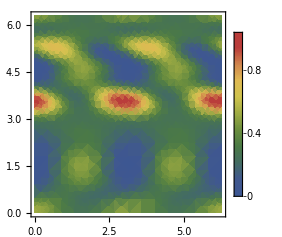

```mathematica
DensityPlot[(probBwarAwar+probAwarBwar)/2, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

Computing the Probability of A or B starting a WAR

Pr(War_A) = (|f_B F_A OverTilde[F_B]S⟩ + F_B F_A S⟩ |)^2

Pr(War_B) = (|f_A F_B OverTilde[F_A]S⟩ + F_A F_B S⟩ |)^2

```mathematica
probAwar= FullSimplify[Norm[fb Subscript[F1, B̄] . SB + Subscript[F2, B] Subscript[F2, A]  SA]^2];
```

```mathematica
Plot3D[probAwar,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),PlotRangePadding->None, ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

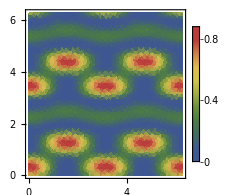

```mathematica
DensityPlot[probAwar, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

```mathematica
probBwar= FullSimplify[Norm[Subscript[F1, A] Subscript[F1, B].SB+ fa Subscript[F2, Ā]  SA]^2];
```

```mathematica
NormConst=1.5;
```

```mathematica
Plot3D[probBwar/NormConst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),PlotRangePadding->None, ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

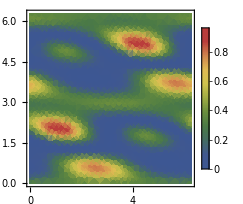

```mathematica
DensityPlot[probBwar/NormConst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic]
```

Finding the Probability of Two Counties Engaging into Capitulation

CAPITULATION OF B

Pr(Cap_B) = (|OverTilde[f_B]F_A OverTilde[F_B]S⟩ + OverTilde[F_B]F_A S⟩ |)^2

Pr( Cap_B| Bstarted) = (|OverTilde[f_B]F_A OverTilde[F_B]S⟩ |)^2

Pr(Cap_B|Astarted) = (|OverTilde[F_B]F_A S⟩ |)^2

```mathematica
probCapB = FullSimplify[Norm[fnotb Subscript[F1, B̄] . SB +Subscript[F2, B̄] Subscript[F2, A]  SA]^2]
```

1/2 (Cos[Re[ϕ]]^2 Sin[Re[θ]]^2 (1+Sin[4 Re[ϕ]])+(Cos[Re[θ]] Sin[Re[ϕ]] (Cos[2 Re[ϕ]]-Sin[2 Re[ϕ]])+Sin[Re[θ+ϕ]])^2)

```mathematica
probCapBBFirst =  FullSimplify[Norm[fnotb Subscript[F1, B̄] . SB ]^2]
```

1/2 Sin[Re[θ+ϕ]]^2

```mathematica
probCapBAFirst =  FullSimplify[Norm[Subscript[F2, B̄] Subscript[F2, A]  SA ]^2];
```

```mathematica
Plot3D[probCapBBFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),PlotRangePadding->None, ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

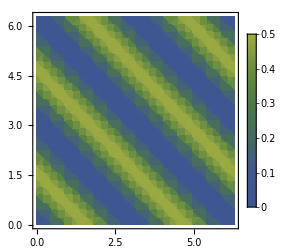

```mathematica
DensityPlot[{probCapBBFirst}, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow", PlotLegends->Automatic,ColorFunctionScaling->False, PlotRange->{0,1} ]
```

```mathematica
Plot3D[probCapBAFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),PlotRange->{0,1},ColorFunctionScaling->False]
```

-Graphics3D-

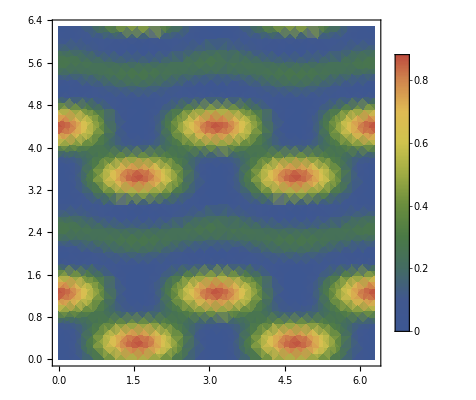

```mathematica
DensityPlot[probCapBAFirst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic,PlotRange->{0,1},ColorFunctionScaling->False]
```

CAPITULATION OF A

Pr(Cap_A) = (|OverTilde[F_A]F_B S⟩ + OverTilde[f_A]F_B OverTilde[F_A]S⟩ |)^2

Pr(Cap_A | Astarted) = (| OverTilde[f_A]F_B OverTilde[F_A]S⟩ |)^2

Pr(Cap_A | Bstarted) = (|OverTilde[F_A]F_B S⟩  |)^2

```mathematica
probCapA = FullSimplify[Norm[Subscript[F1, A] Subscript[F1, B].SB +fnota Subscript[F2, Ā]  SA]^2]
```

```mathematica
probCapABFirst = FullSimplify[Norm[Subscript[F1, A] Subscript[F1, B].SB]^2];
```

```mathematica
probCapAAFirst = FullSimplify[Norm[fnota Subscript[F2, Ā]  SA]^2];
```

```mathematica
Plot3D[probCapABFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]), ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

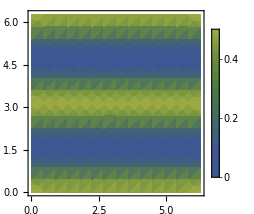

```mathematica
DensityPlot[probCapABFirst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic, ColorFunctionScaling->False,PlotRange->{0,1}]
```

```mathematica
Plot3D[probCapAAFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]), ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

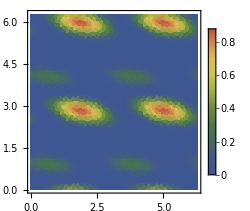

```mathematica
DensityPlot[probCapAAFirst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic, ColorFunctionScaling->False,PlotRange->{0,1}]
```

```mathematica
Negotiation
```

Pr(Neg) = (|OverTilde[F_A]OverTilde[F_B]S⟩ + OverTilde[F_B]OverTilde[F_A]S⟩  |)^2

Pr(Neg | B) = (|OverTilde[F_A]OverTilde[F_B]S⟩   |)^2

Pr(Neg | A) = (|OverTilde[F_B]OverTilde[F_A]S⟩   |)^2

```mathematica
ProbNeg = FullSimplify[ Norm[Subscript[F1, Ā] Subscript[F1, B̄].SB +Subscript[F2, B̄] Subscript[F2, Ā]  SA]]^2;
```

```mathematica
ProbNegBFirst = FullSimplify[ Norm[Subscript[F1, Ā] Subscript[F1, B̄].SB ]]^2;
```

```mathematica
ProbNegAFirst = FullSimplify[ Norm[Subscript[F2, B̄] Subscript[F2, Ā]  SA ]]^2;
```

```mathematica
Plot3D[ProbNegBFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

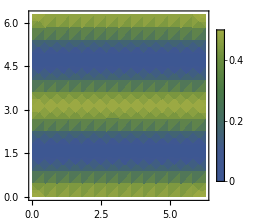

```mathematica
DensityPlot[ProbNegBFirst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic,ColorFunctionScaling->False,PlotRange->{0,1}]
```

```mathematica
Plot3D[ProbNegAFirst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

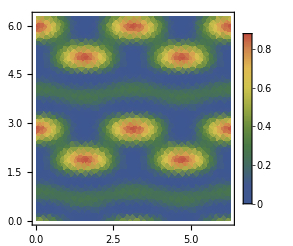

```mathematica
DensityPlot[ProbNegAFirst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic,ColorFunctionScaling->False,PlotRange->{0,1}]
```

```mathematica
NormConst = 2.6;
```

```mathematica
Plot3D[ProbNeg/NormConst,{θ,0,2π},{ϕ,0,2π},Boxed->False, AxesLabel->{Style["θ_(player B)",16],Style["ϕ_(player A)",16],Style["Prob",16]},Mesh->None,ColorFunction->(ColorData["DarkRainbow"]),ColorFunctionScaling->False,PlotRange->{0,1}]
```

-Graphics3D-

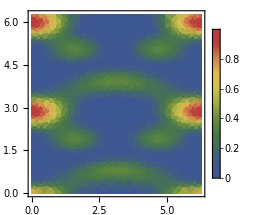

```mathematica
DensityPlot[ProbNeg/NormConst, {θ,0,2π},{ϕ,0,2π},Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}},ColorFunction->"DarkRainbow",PlotLegends->Automatic,ColorFunctionScaling->False,PlotRange->{0,1}]
```